```mathematica
l1={0,1,1};
l2={2,-1,√5};
l3={2,3,-√13};
```

```mathematica
circles=Table[{1,1,r^2},{r,1,20}];
circles//TableForm
```

1 | 1 | 1
1 | 1 | 4
1 | 1 | 9
1 | 1 | 16
1 | 1 | 25
1 | 1 | 36
1 | 1 | 49
1 | 1 | 64
1 | 1 | 81
1 | 1 | 100
1 | 1 | 121
1 | 1 | 144
1 | 1 | 169
1 | 1 | 196
1 | 1 | 225
1 | 1 | 256
1 | 1 | 289
1 | 1 | 324
1 | 1 | 361
1 | 1 | 400

```mathematica
window={{-14,14},{-10,10}};
wndx={x,window[[1,1]],window[[1,2]]};
wndy={y,window[[2,1]],window[[2,2]]};
```

```mathematica
DrawLine[{a_,b_,c_}]:=ContourPlot[
a x + b y +c==0,
Evaluate[wndx],
Evaluate[wndy],
AspectRatio->Automatic
]
```

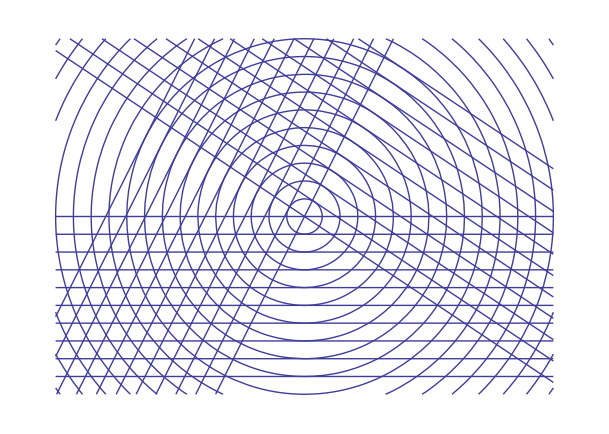

```mathematica
Show[
Table[
ContourPlot[
x^2+y^2==r^2,
Evaluate[wndx],
Evaluate[wndy],
Frame->False,
AspectRatio->Automatic
],
{r,1,100}
],
DrawLine/@Table[l1*{1,1,r},{r,0,10}],
DrawLine/@Table[l2*{1,1,r},{r,0,10}],
DrawLine/@Table[l3*{1,1,r},{r,0,10}]
]
```